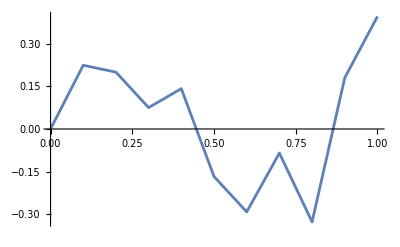

```mathematica
(*uloha 0*)
T=1;
PK=10;
dt=T/PK;
eps=Table[RandomReal[NormalDistribution[0,1]],{i,1,PK}];
w[0]=0;
Do[dw=eps[[i]]*Sqrt[dt];w[i]=w[i-1]+dw,
{i,1,PK}]
sim1=Table[{i*dt,w[i]},{i,0,PK}];
ListPlot[sim1,Joined->True,PlotRange->All]
```

```mathematica
(*uloha 1*)
```

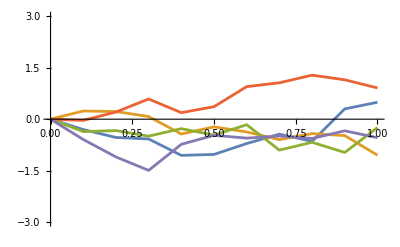

```mathematica
T=1;
PK=10;
dt=T/PK;
X=5; 

colors=ColorData[97,"ColorList"];

GenerateW[]:=Module[{eps,w},eps=Table[RandomReal[NormalDistribution[0,1]],{i,1,PK}];
w[0]=0;
Do[dw=eps[[i]]*Sqrt[dt];
w[i]=w[i-1]+dw,{i,1,PK}];
Table[{i*dt,w[i]},{i,0,PK}]];

simulations=Table[ListPlot[GenerateW[],Joined->True,PlotRange->{-3, 3},PlotStyle->colors[[Mod[j,Length[colors],1]]]],{j,1,X}];

Show[simulations]
```

```mathematica
(*uloha 2*)
```

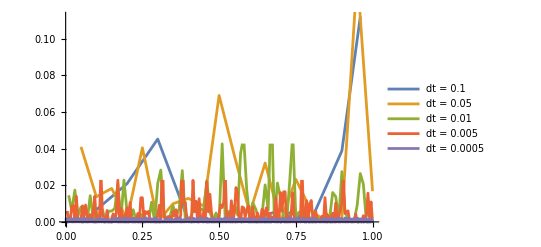

```mathematica
T=1;
X=1; (*Počet simulácií*)
dtList={0.1,0.05,0.01,0.005, 0.0005}; 

colors=ColorData[97,"ColorList"];

GenerateDwSquared[dt_]:=Module[{PK,eps,dw,dwSquared},
PK=Round[T/dt];
eps=Table[RandomReal[NormalDistribution[0,1]],{i,1,PK}];
dwSquared=Table[eps[[i]]^2*dt,{i,1,PK}];
Table[{i*dt,dwSquared[[i]]},{i,1,PK}]];


simulations=Table[ListPlot[GenerateDwSquared[dtList[[k]]],Joined->True,PlotRange->Automatic,PlotStyle->colors[[Mod[k,Length[colors],1]]],PlotLegends->Placed[{"dt = "<>ToString[dtList[[k]]]},Bottom]],{k,1,Length[dtList]}];

Show[simulations]
```

```mathematica
(*uloha 3*)
```

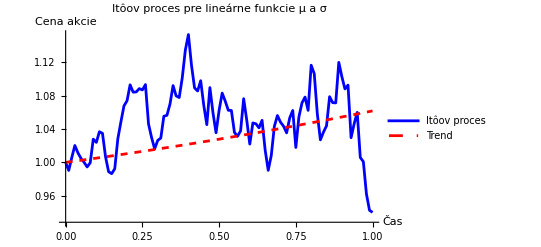

```mathematica
T=1; 
PK=100; 
dt=T/PK;

mu0=0.05; (*Konštantná zložka trendu*)
mu1=0.01; (*Lineárna časť trendu*)
sigma0=0.2; (*Konštantná volatilita*)
sigma1=0.05; (*Lineárna zložka volatility*)

S0=1; 

eps=Table[RandomReal[NormalDistribution[0,1]],{i,1,PK}];

S[0]=S0;
Do[mu=(mu0+mu1*i*dt);(*Funkcia mi*)sigma=(sigma0+sigma1*i*dt);(*Funkcia sigma*)dW=eps[[i]]*Sqrt[dt];
dS=mu*S[i-1]*dt+sigma*S[i-1]*dW;
S[i]=S[i-1]+dS,{i,1,PK}];

trend=Table[S0*Exp[(mu0+mu1*t)*t],{t,0,T,dt}];

time=Table[i*dt,{i,0,PK}];

ListLinePlot[{Transpose[{time,Table[S[i],{i,0,PK}]}],Transpose[{time,trend}]},PlotStyle->{Blue,{Red,Dashed}},PlotLegends->Placed[{"Itôov proces","Trend"},Bottom],PlotRange->All,AxesLabel->{"Čas","Cena akcie"},PlotLabel->"Itôov proces pre lineárne funkcie μ a σ"]
```